```mathematica
data0 = Import["C:\\研究\\多変量解析入門\\heat-portland-cement.xlsx"];
```

```mathematica
Length[data0]
```

1

```mathematica
data=First[data0];
```

```mathematica
Length[data]
```

14

```mathematica
data
```

{{x1,x2,x3,x4,y},{7.,26.,6.,60.,78.5},{1.,29.,15.,52.,74.3},{11.,56.,8.,20.,104.3},{11.,31.,8.,47.,87.6},{7.,52.,6.,33.,95.9},{11.,55.,9.,22.,109.2},{3.,71.,17.,6.,102.7},{1.,31.,22.,44.,72.5},{2.,54.,18.,22.,93.1},{21.,47.,4.,26.,115.9},{1.,40.,23.,34.,83.8},{11.,66.,9.,12.,113.3},{10.,68.,8.,12.,109.4}}

```mathematica
data = Drop[data,1];
```

```mathematica
(* p1=ListPlot[data,Frame->True,FrameLabel->{"直径(cm)","高さ(m)"},FrameStyle->16]*)
```

```mathematica
Transpose[Transpose[data][[{1,5}]]]
```

{{7.,78.5},{1.,74.3},{11.,104.3},{11.,87.6},{7.,95.9},{11.,109.2},{3.,102.7},{1.,72.5},{2.,93.1},{21.,115.9},{1.,83.8},{11.,113.3},{10.,109.4}}

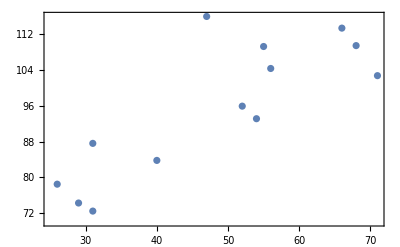

```mathematica
ListPlot[Transpose[Transpose[data][[{2,5}]]],Frame->True]
```

```mathematica
MatrixForm[Correlation[Transpose[Transpose[data][[{1,5}]]]]]
```

(1. | 0.730717
0.730717 | 1.)

```mathematica
MatrixForm[Correlation[data]]
```

(1. | 0.228579 | -0.824134 | -0.245445 | 0.730717
0.228579 | 1. | -0.139242 | -0.972955 | 0.816253
-0.824134 | -0.139242 | 1. | 0.029537 | -0.534671
-0.245445 | -0.972955 | 0.029537 | 1. | -0.821305
0.730717 | 0.816253 | -0.534671 | -0.821305 | 1.)

```mathematica
(* 偏相関関数をつくる *)
```

```mathematica
num= Length[data]
```

13

```mathematica
yvalues = Transpose[data][[5]]
```

{78.5,74.3,104.3,87.6,95.9,109.2,102.7,72.5,93.1,115.9,83.8,113.3,109.4}

```mathematica
xvalues = Transpose[data][[3]]
```

{6.,15.,8.,8.,6.,9.,17.,22.,18.,4.,23.,9.,8.}

```mathematica
Correlation[xvalues,yvalues]
```

-0.534671

```mathematica
xremobed=Transpose[data][[{1,2,4}]]
```

{{7.,1.,11.,11.,7.,11.,3.,1.,2.,21.,1.,11.,10.},{26.,29.,56.,31.,52.,55.,71.,31.,54.,47.,40.,66.,68.},{60.,52.,20.,47.,33.,22.,6.,44.,22.,26.,34.,12.,12.}}

```mathematica
cv=ConstantArray[1,num];
```

```mathematica
Xp=Transpose[Prepend[xremobed,cv]];
```

```mathematica
MatrixForm[Xp]
```

(1 | 7. | 26. | 60.
1 | 1. | 29. | 52.
1 | 11. | 56. | 20.
1 | 11. | 31. | 47.
1 | 7. | 52. | 33.
1 | 11. | 55. | 22.
1 | 3. | 71. | 6.
1 | 1. | 31. | 44.
1 | 2. | 54. | 22.
1 | 21. | 47. | 26.
1 | 1. | 40. | 34.
1 | 11. | 66. | 12.
1 | 10. | 68. | 12.)

```mathematica
Xpt = Transpose[Xp];
```

```mathematica
projmat=IdentityMatrix[Length[data]]- Xp.Inverse[Xpt.Xp].Xpt;
```

```mathematica
projmat.projmat - projmat//Chop ;
```

```mathematica
Correlation[xvalues,yvalues]
```

-0.534671

```mathematica
Correlation[projmat.xvalues,projmat.yvalues]
```

0.0476865

```mathematica
Correlation[projmat.xvalues,projmat.yvalues]
```

0.0476865

```mathematica
(*  Module にする*)
```

```mathematica
pcorr[data_,numx_,numy_,numother_]:=Module[{num,xvalues,yvalues,xremobed,cv,Xp,Xpt,projmat},
num= Length[data];
yvalues = Transpose[data][[numy]];
xvalues = Transpose[data][[numx]];
xremobed=Transpose[data][[numother]];
cv=ConstantArray[1,num];
Xp=Transpose[Prepend[xremobed,cv]];
Xpt = Transpose[Xp];
projmat=IdentityMatrix[Length[data]]- Xp.Inverse[Xpt.Xp].Xpt;
Correlation[projmat.xvalues,projmat.yvalues]]
```

```mathematica
pcorr[data,3,5,{1,2,4}]
```

0.0476865

```mathematica
pcorrlist={pcorr[data,1,5,{2,3,4}],pcorr[data,2,5,{1,3,4}],pcorr[data,3,5,{1,2,4}],pcorr[data,4,5,{1,2,3}]}
```

{0.592933,0.241809,0.0476865,-0.0716483}

```mathematica
MatrixForm[Correlation[data]]
```

(1. | 0.228579 | -0.824134 | -0.245445 | 0.730717
0.228579 | 1. | -0.139242 | -0.972955 | 0.816253
-0.824134 | -0.139242 | 1. | 0.029537 | -0.534671
-0.245445 | -0.972955 | 0.029537 | 1. | -0.821305
0.730717 | 0.816253 | -0.534671 | -0.821305 | 1.)

```mathematica
(* 偏相関　ここまで*)
```

```mathematica
(* 最初に FindFit　でやってみる *)
```

```mathematica
model1234 = β0 + β1 x1 + β2 x2 + β3 x3 + β4 x4;
```

```mathematica
ans1234=FindFit[data,model1234,{β0,β1,β2,β3,β4},{x1,x2,x3,x4}]
```

{β0→62.4054,β1→1.5511,β2→0.510168,β3→0.101909,β4→-0.144061}

```mathematica
(* x3 を落としたモデル: data から x3 を落とす必要なし*)
```

```mathematica
model124 = β0 + β1 x1 + β2 x2  + β4 x4;
```

```mathematica
ans124=FindFit[data,model124,{β0,β1,β2,β4},{x1,x2,x3,x4}]
```

{β0→71.6483,β1→1.45194,β2→0.41611,β4→-0.23654}

```mathematica
(* 最尤法 パラメター　βs = {β0,β1,β2,β3,β4 }　の求め方は結局最小２乗法と同じ *)
```

```mathematica
num= Length[data]
```

13

```mathematica
yvalues = Transpose[data][[5]];
```

```mathematica
xdummy=Transpose[data][[1;;4]]
```

{{7.,1.,11.,11.,7.,11.,3.,1.,2.,21.,1.,11.,10.},{26.,29.,56.,31.,52.,55.,71.,31.,54.,47.,40.,66.,68.},{6.,15.,8.,8.,6.,9.,17.,22.,18.,4.,23.,9.,8.},{60.,52.,20.,47.,33.,22.,6.,44.,22.,26.,34.,12.,12.}}

```mathematica
cv=ConstantArray[1,num];
```

```mathematica
Xmat=Transpose[Prepend[xdummy,cv]];
```

```mathematica
MatrixForm[Xmat]
```

(1 | 7. | 26. | 6. | 60.
1 | 1. | 29. | 15. | 52.
1 | 11. | 56. | 8. | 20.
1 | 11. | 31. | 8. | 47.
1 | 7. | 52. | 6. | 33.
1 | 11. | 55. | 9. | 22.
1 | 3. | 71. | 17. | 6.
1 | 1. | 31. | 22. | 44.
1 | 2. | 54. | 18. | 22.
1 | 21. | 47. | 4. | 26.
1 | 1. | 40. | 23. | 34.
1 | 11. | 66. | 9. | 12.
1 | 10. | 68. | 8. | 12.)

```mathematica
XmatT=Transpose[Xmat];
```

```mathematica
XtX = Transpose[Xmat].Xmat
```

{{13.,97.,626.,153.,390.},{97.,1139.,4922.,769.,2620.},{626.,4922.,33050.,7201.,15739.},{153.,769.,7201.,2293.,4628.},{390.,2620.,15739.,4628.,15062.}}

```mathematica
βs=Inverse[XtX].XmatT.yvalues
```

{62.4054,1.5511,0.510168,0.101909,-0.144061}

```mathematica
ans1234
```

{β0→62.4054,β1→1.5511,β2→0.510168,β3→0.101909,β4→-0.144061}

```mathematica
res1234= yvalues - Xmat.βs
```

{0.00476042,1.5112,-1.67094,-1.7271,0.250756,3.92544,-1.44867,-3.17499,1.37835,0.281548,1.99098,0.972989,-2.29433}

```mathematica
residual=(yvalues - Xmat.βs).(yvalues - Xmat.βs)
```

47.8636

```mathematica
σsq = ((yvalues - Xmat.βs).(yvalues - Xmat.βs))/num
```

3.68182

```mathematica
maxlogl =- num/2 Log[2 π σsq]- num/2
```

-26.9183

```mathematica
aic = -2 maxlogl + 2 (4+2)
```

65.8367

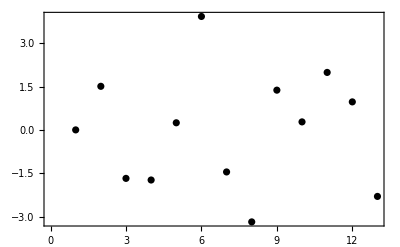

```mathematica
pres=ListPlot[yvalues - Xmat.βs,Frame->True,PlotStyle->Black]
```

```mathematica
(* x3 を抜いてみる *)
```

```mathematica
Xmat124 =Transpose[ Transpose[Xmat][[{1,2,3,5}]]]
```

{{1,7.,26.,60.},{1,1.,29.,52.},{1,11.,56.,20.},{1,11.,31.,47.},{1,7.,52.,33.},{1,11.,55.,22.},{1,3.,71.,6.},{1,1.,31.,44.},{1,2.,54.,22.},{1,21.,47.,26.},{1,1.,40.,34.},{1,11.,66.,12.},{1,10.,68.,12.}}

```mathematica
MatrixForm[Xmat124]
```

(1 | 7. | 26. | 60.
1 | 1. | 29. | 52.
1 | 11. | 56. | 20.
1 | 11. | 31. | 47.
1 | 7. | 52. | 33.
1 | 11. | 55. | 22.
1 | 3. | 71. | 6.
1 | 1. | 31. | 44.
1 | 2. | 54. | 22.
1 | 21. | 47. | 26.
1 | 1. | 40. | 34.
1 | 11. | 66. | 12.
1 | 10. | 68. | 12.)

```mathematica
βs124=Inverse[Transpose[Xmat124].Xmat124].Transpose[Xmat124].yvalues
```

{71.6483,1.45194,0.41611,-0.23654}

```mathematica
ans124
```

{β0→71.6483,β1→1.45194,β2→0.41611,β4→-0.23654}

```mathematica
residual124=(yvalues - Xmat124.βs124).(yvalues - Xmat124.βs124)
```

47.9727

```mathematica
σsq124 = ((yvalues - Xmat124.βs124).(yvalues - Xmat124.βs124))/num
```

3.69021

```mathematica
maxlogl124 =- num/2 Log[2 π σsq124]- num/2
```

-26.9331

```mathematica
aic124= -2 maxlogl124 + 2 (3+2)
```

63.8663

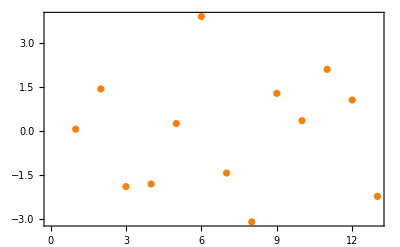

```mathematica
pres124=ListPlot[yvalues - Xmat124.βs124,Frame->True,PlotStyle->Orange]
```

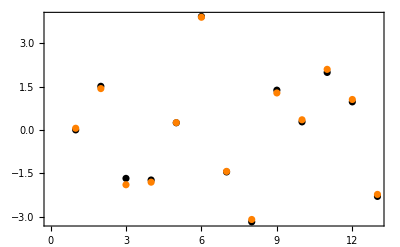

```mathematica
Show[pres,pres124]
```

```mathematica
(* １５通りのモデル　AIC のリスト *)
```

```mathematica
nx =4;
```

```mathematica
Subsets[{1,2,3,4},4]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
Drop[Subsets[{1,2,3,4},4],1]
```

{{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
vc=Sort[Drop[Subsets[{1,2,3,4},4],1]]
```

{{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
yvalues = Transpose[data][[5]];
```

```mathematica
vc[[15]]
```

{1,2,3,4}

```mathematica
cv=ConstantArray[1,num];
```

```mathematica
k=3;
```

```mathematica
vc⟦k⟧
```

{3}

```mathematica
xd=Transpose[data]⟦vc⟦k⟧⟧;
```

```mathematica
Xmat=Transpose[Prepend[xd,cv]];
```

```mathematica
XmatT=Transpose[Xmat];
```

```mathematica
XtX = Transpose[Xmat].Xmat;
```

```mathematica
βs=Inverse[XtX].XmatT.yvalues
```

{110.203,-1.25578}

```mathematica
βs
```

{110.203,-1.25578}

```mathematica
tmp={βs[[1]],miss,miss,miss,miss}
```

{110.203,miss,miss,miss,miss}

```mathematica
pos=vc⟦k⟧+1
```

{4}

```mathematica
tmp[[pos]]= Drop[βs,1]
```

{-1.25578}

```mathematica
tmp
```

{110.203,miss,miss,-1.25578,miss}

```mathematica
σsq = ((yvalues - Xmat.βs).(yvalues - Xmat.βs))/num
```

149.185

```mathematica
maxlogl =- num/2 Log[2 π σsq]- num/2
```

-50.9799

```mathematica
aic = -2 maxlogl + 2 (Length[vc⟦k⟧]+2)
```

107.96

```mathematica
aics[k_]:=Module[{cv,xd,Xmat,XmatT,XtX,βs,σsq,maxlogl,aic},
cv=ConstantArray[1,num];
xd=Transpose[data]⟦vc⟦k⟧⟧;
Xmat=Transpose[Prepend[xd,cv]];
XmatT=Transpose[Xmat];
XtX = Transpose[Xmat].Xmat;
βs=Inverse[XtX].XmatT.yvalues;
σsq = ((yvalues - Xmat.βs).(yvalues - Xmat.βs))/num;
maxlogl =- num/2 Log[2 π σsq]- num/2;
aic = -2 maxlogl + 2 (Length[vc⟦k⟧]+2);
{vc⟦k⟧,σsq,maxlogl,aic}
]
```

```mathematica
aics[13]
```

{{1,3,4},3.91047,-27.31,64.62}

```mathematica
Prepend[aics[13],13]
```

{13,{1,3,4},3.91047,-27.31,64.62}

```mathematica
Table[aics[k],{k,15,1,-1}]
```

{{{1,2,3,4},3.68182,-26.9183,65.8367},{{2,3,4},5.67804,-29.7341,69.4683},{{1,3,4},3.91047,-27.31,64.62},{{1,2,4},3.69021,-26.9331,63.8663},{{1,2,3},3.70082,-26.9518,63.9036},{{3,4},13.5183,-35.3725,78.745},{{2,4},66.8369,-45.7609,99.5217},{{2,3},31.9571,-40.9648,89.9295},{{1,4},5.75093,-29.8171,67.6341},{{1,3},94.3902,-48.0045,104.009},{{1,2},4.45419,-28.1562,64.3124},{{4},67.9898,-45.872,97.744},{{3},149.185,-50.9799,107.96},{{2},69.7182,-46.0352,98.0704},{{1},97.3605,-48.2059,102.412}}

```mathematica
Table[Prepend[aics[k],k],{k,15,1,-1}]
```

{{15,{1,2,3,4},3.68182,-26.9183,65.8367},{14,{2,3,4},5.67804,-29.7341,69.4683},{13,{1,3,4},3.91047,-27.31,64.62},{12,{1,2,4},3.69021,-26.9331,63.8663},{11,{1,2,3},3.70082,-26.9518,63.9036},{10,{3,4},13.5183,-35.3725,78.745},{9,{2,4},66.8369,-45.7609,99.5217},{8,{2,3},31.9571,-40.9648,89.9295},{7,{1,4},5.75093,-29.8171,67.6341},{6,{1,3},94.3902,-48.0045,104.009},{5,{1,2},4.45419,-28.1562,64.3124},{4,{4},67.9898,-45.872,97.744},{3,{3},149.185,-50.9799,107.96},{2,{2},69.7182,-46.0352,98.0704},{1,{1},97.3605,-48.2059,102.412}}

```mathematica
items ={"k","説明変数","σ^2","最大対数尤度","AIC"};
```

```mathematica
Grid[Prepend[Table[Prepend[aics[k],k],{k,15,1,-1}],items],Frame->All]
```

k | 説明変数 | σ^2 | 最大対数尤度 | AIC
15 | {1,2,3,4} | 3.68182 | -26.9183 | 65.8367
14 | {2,3,4} | 5.67804 | -29.7341 | 69.4683
13 | {1,3,4} | 3.91047 | -27.31 | 64.62
12 | {1,2,4} | 3.69021 | -26.9331 | 63.8663
11 | {1,2,3} | 3.70082 | -26.9518 | 63.9036
10 | {3,4} | 13.5183 | -35.3725 | 78.745
9 | {2,4} | 66.8369 | -45.7609 | 99.5217
8 | {2,3} | 31.9571 | -40.9648 | 89.9295
7 | {1,4} | 5.75093 | -29.8171 | 67.6341
6 | {1,3} | 94.3902 | -48.0045 | 104.009
5 | {1,2} | 4.45419 | -28.1562 | 64.3124
4 | {4} | 67.9898 | -45.872 | 97.744
3 | {3} | 149.185 | -50.9799 | 107.96
2 | {2} | 69.7182 | -46.0352 | 98.0704
1 | {1} | 97.3605 | -48.2059 | 102.412

```mathematica
Grid[Prepend[Sort[Table[Prepend[aics[k],k],{k,15,1,-1}],#1[[5]]<#2[[5]]&],items],Frame->All]
```

k | 説明変数 | σ^2 | 最大対数尤度 | AIC
12 | {1,2,4} | 3.69021 | -26.9331 | 63.8663
11 | {1,2,3} | 3.70082 | -26.9518 | 63.9036
5 | {1,2} | 4.45419 | -28.1562 | 64.3124
13 | {1,3,4} | 3.91047 | -27.31 | 64.62
15 | {1,2,3,4} | 3.68182 | -26.9183 | 65.8367
7 | {1,4} | 5.75093 | -29.8171 | 67.6341
14 | {2,3,4} | 5.67804 | -29.7341 | 69.4683
10 | {3,4} | 13.5183 | -35.3725 | 78.745
8 | {2,3} | 31.9571 | -40.9648 | 89.9295
4 | {4} | 67.9898 | -45.872 | 97.744
2 | {2} | 69.7182 | -46.0352 | 98.0704
9 | {2,4} | 66.8369 | -45.7609 | 99.5217
1 | {1} | 97.3605 | -48.2059 | 102.412
6 | {1,3} | 94.3902 | -48.0045 | 104.009
3 | {3} | 149.185 | -50.9799 | 107.96

```mathematica
(* パラメタも出力*)
```

```mathematica
aics2[k_]:=Module[{cv,xd,Xmat,XmatT,XtX,tmp,βs,pos,σsq,maxlogl,aic},
cv=ConstantArray[1,num];
xd=Transpose[data]⟦vc⟦k⟧⟧;
Xmat=Transpose[Prepend[xd,cv]];
XmatT=Transpose[Xmat];
XtX = Transpose[Xmat].Xmat;
βs=Inverse[XtX].XmatT.yvalues;
tmp={βs[[1]],"missing","missing","missing","missing"};
pos=vc⟦k⟧+1;
tmp[[pos]]= Drop[βs,1];
σsq = ((yvalues - Xmat.βs).(yvalues - Xmat.βs))/num;
maxlogl =- num/2 Log[2 π σsq]- num/2;
aic = -2 maxlogl + 2 (Length[vc⟦k⟧]+2);
{vc⟦k⟧,tmp,σsq,maxlogl,aic}
]
```

```mathematica
aics2[10]
```

{{3,4},{131.282,missing,missing,-1.19985,-0.7246},13.5183,-35.3725,78.745}

```mathematica
Grid[Table[Prepend[aics2[k],k],{k,15,1,-1}]];
```

```mathematica
items2={"k","説明変数","βs","σ^2","最大対数尤度","AIC"};
```

```mathematica
pcorrlist
```

{0.592933,0.241809,0.0476865,-0.0716483}

```mathematica
Grid[Prepend[Table[Prepend[aics2[k],k],{k,15,1,-1}],items2],Frame->All]
```

k | 説明変数 | βs | σ^2 | 最大対数尤度 | AIC
15 | {1,2,3,4} | {62.4054,1.5511,0.510168,0.101909,-0.144061} | 3.68182 | -26.9183 | 65.8367
14 | {2,3,4} | {203.642,missing,-0.923416,-1.44797,-1.55704} | 5.67804 | -29.7341 | 69.4683
13 | {1,3,4} | {111.684,1.05185,missing,-0.410043,-0.642796} | 3.91047 | -27.31 | 64.62
12 | {1,2,4} | {71.6483,1.45194,0.41611,missing,-0.23654} | 3.69021 | -26.9331 | 63.8663
11 | {1,2,3} | {48.1936,1.69589,0.656915,0.250018,missing} | 3.70082 | -26.9518 | 63.9036
10 | {3,4} | {131.282,missing,missing,-1.19985,-0.7246} | 13.5183 | -35.3725 | 78.745
9 | {2,4} | {94.1601,missing,0.310905,missing,-0.456942} | 66.8369 | -45.7609 | 99.5217
8 | {2,3} | {72.0747,missing,0.73133,-1.00839,missing} | 31.9571 | -40.9648 | 89.9295
7 | {1,4} | {103.097,1.43996,missing,missing,-0.613954} | 5.75093 | -29.8171 | 67.6341
6 | {1,3} | {72.349,2.31247,missing,0.494468,missing} | 94.3902 | -48.0045 | 104.009
5 | {1,2} | {52.5773,1.46831,0.66225,missing,missing} | 4.45419 | -28.1562 | 64.3124
4 | {4} | {117.568,missing,missing,missing,-0.738162} | 67.9898 | -45.872 | 97.744
3 | {3} | {110.203,missing,missing,-1.25578,missing} | 149.185 | -50.9799 | 107.96
2 | {2} | {57.4237,missing,0.789125,missing,missing} | 69.7182 | -46.0352 | 98.0704
1 | {1} | {81.4793,1.86875,missing,missing,missing} | 97.3605 | -48.2059 | 102.412

```mathematica
(* AIC で sort*)
```

```mathematica
Grid[Prepend[Sort[Table[Prepend[aics2[k],k],{k,15,1,-1}],#1[[6]]<#2[[6]]&],items2],Frame->All]
```

k | 説明変数 | βs | σ^2 | 最大対数尤度 | AIC
12 | {1,2,4} | {71.6483,1.45194,0.41611,missing,-0.23654} | 3.69021 | -26.9331 | 63.8663
11 | {1,2,3} | {48.1936,1.69589,0.656915,0.250018,missing} | 3.70082 | -26.9518 | 63.9036
5 | {1,2} | {52.5773,1.46831,0.66225,missing,missing} | 4.45419 | -28.1562 | 64.3124
13 | {1,3,4} | {111.684,1.05185,missing,-0.410043,-0.642796} | 3.91047 | -27.31 | 64.62
15 | {1,2,3,4} | {62.4054,1.5511,0.510168,0.101909,-0.144061} | 3.68182 | -26.9183 | 65.8367
7 | {1,4} | {103.097,1.43996,missing,missing,-0.613954} | 5.75093 | -29.8171 | 67.6341
14 | {2,3,4} | {203.642,missing,-0.923416,-1.44797,-1.55704} | 5.67804 | -29.7341 | 69.4683
10 | {3,4} | {131.282,missing,missing,-1.19985,-0.7246} | 13.5183 | -35.3725 | 78.745
8 | {2,3} | {72.0747,missing,0.73133,-1.00839,missing} | 31.9571 | -40.9648 | 89.9295
4 | {4} | {117.568,missing,missing,missing,-0.738162} | 67.9898 | -45.872 | 97.744
2 | {2} | {57.4237,missing,0.789125,missing,missing} | 69.7182 | -46.0352 | 98.0704
9 | {2,4} | {94.1601,missing,0.310905,missing,-0.456942} | 66.8369 | -45.7609 | 99.5217
1 | {1} | {81.4793,1.86875,missing,missing,missing} | 97.3605 | -48.2059 | 102.412
6 | {1,3} | {72.349,2.31247,missing,0.494468,missing} | 94.3902 | -48.0045 | 104.009
3 | {3} | {110.203,missing,missing,-1.25578,missing} | 149.185 | -50.9799 | 107.96

```mathematica
(* σ^2  で sort *)
```

```mathematica
Grid[Prepend[Sort[Table[Prepend[aics2[k],k],{k,15,1,-1}],#1[[4]]<#2[[4]]&],items2],Frame->All]
```

k | 説明変数 | βs | σ^2 | 最大対数尤度 | AIC
15 | {1,2,3,4} | {62.4054,1.5511,0.510168,0.101909,-0.144061} | 3.68182 | -26.9183 | 65.8367
12 | {1,2,4} | {71.6483,1.45194,0.41611,missing,-0.23654} | 3.69021 | -26.9331 | 63.8663
11 | {1,2,3} | {48.1936,1.69589,0.656915,0.250018,missing} | 3.70082 | -26.9518 | 63.9036
13 | {1,3,4} | {111.684,1.05185,missing,-0.410043,-0.642796} | 3.91047 | -27.31 | 64.62
5 | {1,2} | {52.5773,1.46831,0.66225,missing,missing} | 4.45419 | -28.1562 | 64.3124
14 | {2,3,4} | {203.642,missing,-0.923416,-1.44797,-1.55704} | 5.67804 | -29.7341 | 69.4683
7 | {1,4} | {103.097,1.43996,missing,missing,-0.613954} | 5.75093 | -29.8171 | 67.6341
10 | {3,4} | {131.282,missing,missing,-1.19985,-0.7246} | 13.5183 | -35.3725 | 78.745
8 | {2,3} | {72.0747,missing,0.73133,-1.00839,missing} | 31.9571 | -40.9648 | 89.9295
9 | {2,4} | {94.1601,missing,0.310905,missing,-0.456942} | 66.8369 | -45.7609 | 99.5217
4 | {4} | {117.568,missing,missing,missing,-0.738162} | 67.9898 | -45.872 | 97.744
2 | {2} | {57.4237,missing,0.789125,missing,missing} | 69.7182 | -46.0352 | 98.0704
6 | {1,3} | {72.349,2.31247,missing,0.494468,missing} | 94.3902 | -48.0045 | 104.009
1 | {1} | {81.4793,1.86875,missing,missing,missing} | 97.3605 | -48.2059 | 102.412
3 | {3} | {110.203,missing,missing,-1.25578,missing} | 149.185 | -50.9799 | 107.96

```mathematica
(* 残差も出力 *)
```

```mathematica
aics3[k_]:=Module[{cv,xd,Xmat,XmatT,XtX,βs,res,σsq,maxlogl,aic},
cv=ConstantArray[1,num];
xd=Transpose[data]⟦vc⟦k⟧⟧;
Xmat=Transpose[Prepend[xd,cv]];
XmatT=Transpose[Xmat];
XtX = Transpose[Xmat].Xmat;
βs=Inverse[XtX].XmatT.yvalues;
res = yvalues - Xmat.βs;
σsq = ((yvalues - Xmat.βs).(yvalues - Xmat.βs))/num;
maxlogl =- num/2 Log[2 π σsq]- num/2;
aic = -2 maxlogl + 2 (Length[vc⟦k⟧]+2);
{vc⟦k⟧,σsq,maxlogl,aic,res}
]
```

```mathematica
aics3[15]
```

{{1,2,3,4},3.68182,-26.9183,65.8367,{0.00476042,1.5112,-1.67094,-1.7271,0.250756,3.92544,-1.44867,-3.17499,1.37835,0.281548,1.99098,0.972989,-2.29433}}

```mathematica
vc[[12]]
```

{1,2,4}

```mathematica
Head[ToString[ToExpression[vc[[12]]]]]
```

String

```mathematica
(* 残差をplot *)
```

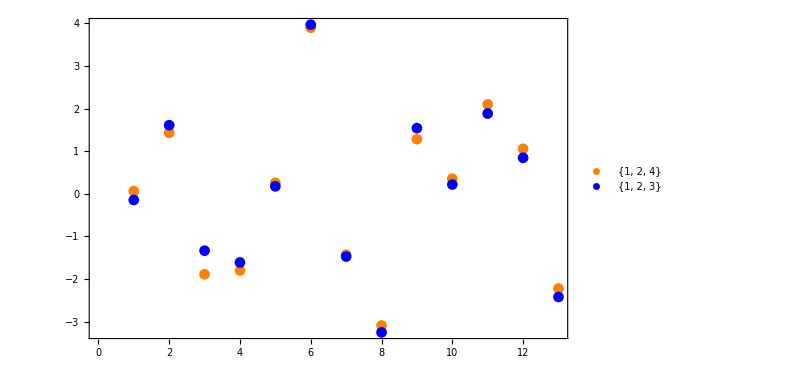

```mathematica
k1=12;k2=11;
ListPlot[{aics3[k1][[5]],aics3[k2][[5]]},Frame->True,PlotStyle->{Orange,Blue},
PlotLegends->{ToString[ToExpression[vc[[k1]]]],ToString[ToExpression[vc[[k2]]]]},ImageSize->600]
```

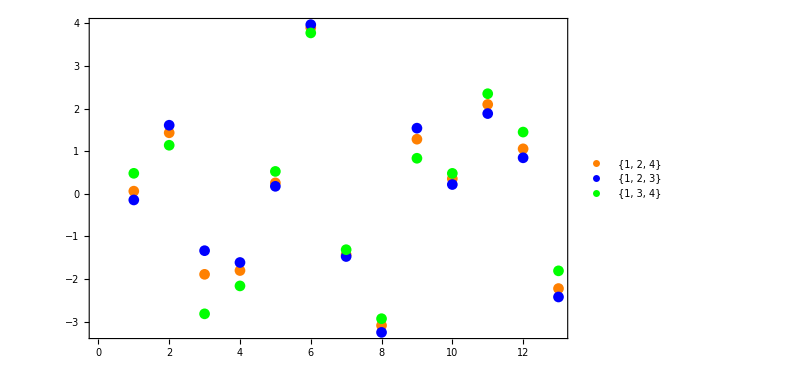

```mathematica
k1=12;k2=11;k3=13;
ListPlot[{aics3[k1][[5]],aics3[k2][[5]],aics3[k3][[5]]},Frame->True,PlotStyle->{Orange,Blue,Green},
PlotLegends->{ToString[ToExpression[vc[[k1]]]],ToString[ToExpression[vc[[k2]]]],
ToString[ToExpression[vc[[k3]]]]},ImageSize->600]
```

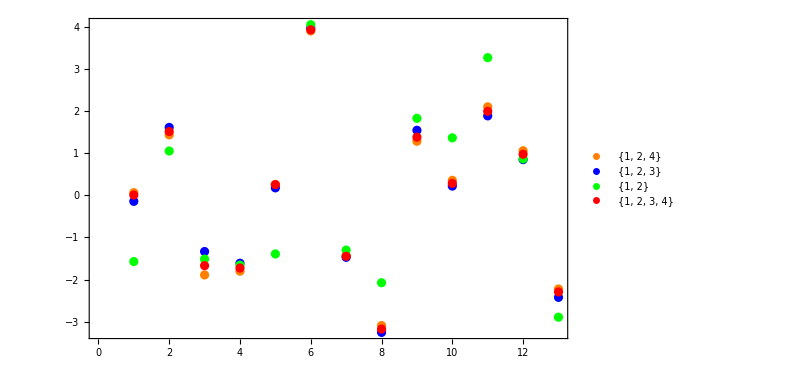

```mathematica
k1=12;k2=11;k3=5;k4=15;
ListPlot[{aics3[k1][[5]],aics3[k2][[5]],aics3[k3][[5]],aics3[k4][[5]]},Frame->True,PlotStyle->{Orange,Blue,Green,Red},
PlotLegends->{ToString[ToExpression[vc[[k1]]]],ToString[ToExpression[vc[[k2]]]],
ToString[ToExpression[vc[[k3]]]],ToString[ToExpression[vc[[k4]]]]},ImageSize->600]
```

```mathematica
model=First[{aics2[15][[2]]/."missing"->0}.{1,x1,x2,x3,x4}]
```

62.4054+1.5511 x1+0.510168 x2+0.101909 x3-0.144061 x4

```mathematica
??NonlinearModelFit
```

```mathematica
model1234
```

β0+x1 β1+x2 β2+x3 β3+x4 β4

```mathematica
fit1234=NonlinearModelFit[data,model1234,{β0,β1,β2,β3,β4},{x1,x2,x3,x4}]
```

FittedModel[62.4054+1.5511 x1+0.510168 x2+0.101909 x3-0.144061 x4]

```mathematica
ans1234
```

{β0→62.4054,β1→1.5511,β2→0.510168,β3→0.101909,β4→-0.144061}

```mathematica
fit1234["FitResiduals"]
```

{0.00476042,1.5112,-1.67094,-1.7271,0.250756,3.92544,-1.44867,-3.17499,1.37835,0.281548,1.99098,0.972989,-2.29433}

```mathematica
fit1234["FitResiduals"]
```

{0.00476042,1.5112,-1.67094,-1.7271,0.250756,3.92544,-1.44867,-3.17499,1.37835,0.281548,1.99098,0.972989,-2.29433}

```mathematica
aic1234 = fit1234["AIC"]
```

67.1483

```mathematica
aics[15][[4]]
```

65.8367

```mathematica
aic1234-aics[15][[4]]
```

1.3116

```mathematica
(* *)
```

```mathematica
model124
```

β0+x1 β1+x2 β2+x4 β4

```mathematica
fit124=NonlinearModelFit[data,model124,{β0,β1,β2,β4},{x1,x2,x3,x4}]
```

FittedModel[71.6483+1.45194 x1+0.41611 x2-0.23654 x4]

```mathematica
ans124
```

{β0→71.6483,β1→1.45194,β2→0.41611,β4→-0.23654}

```mathematica
aic124 = fit124["AIC"]
```

64.6467

```mathematica
aics[12]
```

{{1,2,4},3.69021,-26.9331,63.8663}

```mathematica
aic124 - aics[12][[4]]
```

0.780422

```mathematica
(* *)
```

```mathematica
model123 = β0 + β1 x1 + β2 x2 + β3 x3 ;
```

```mathematica
fit123=NonlinearModelFit[data,model123,{β0,β1,β2,β3},{x1,x2,x3,x4}]
```

FittedModel[48.1936+1.69589 x1+0.656915 x2+0.250018 x3]

```mathematica
aic123=fit123["AIC"]
```

64.684

```mathematica
aics[11]
```

{{1,2,3},3.70082,-26.9518,63.9036}

```mathematica
aic123 - aics[11][[4]]
```

0.780422